```mathematica
p=0.5;
f[x_]:=x^(p-1)/(x+1)
```

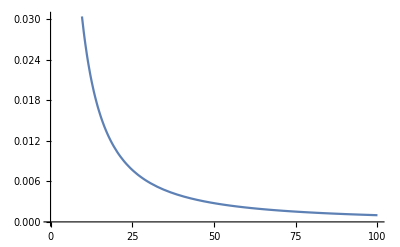

```mathematica
Plot[f[x],{x,0,100}]
```

```mathematica
SommaDiRiemannI[a_,b_,n_]:= ( deltax=(b-a)/2^n;x=a;Somma=0;  For[k=0,k<2^n,k++,Somma+= f[x];x+=deltax]; Somma*=deltax;Return[Somma])
SommaDiRiemannS[a_,b_,n_]:= ( deltax=(b-a)/2^n;x=a+deltax;Somma=0;  For[k=0,k<2^n,k++,Somma+= f[x];x+=deltax]; Somma*=deltax;Return[Somma])
SommaDiRiemann[a_,b_,n_]:= ( SeedRandom[];deltax=(b-a)/2^n;x=a;Somma=0;  For[k=0,k<2^n,k++,Somma+= f[x+deltax*RandomReal[]];x+=deltax]; Somma*=deltax;Return[Somma])
SommaDiRiemannEps[a_,b_,eps_,maxc_,maxn_]:=(n=Ceiling[Log[2,(b-a)/eps]];s2=0;count=0;
Print["----- n= ",n,"\teps= ",eps,"\tmaxc= ",maxc]
Print["----- maxn= ",maxn,"\n"]
While[True,s1=s2;s2=SommaDiRiemann[a,b,n];Print["n=",n,"\tCount=",count,"\tAbs=",Abs[s2-s1],"\ts=",s2];If[Abs[s2-s1]≤eps,count++,count=0];If[count≥maxc,Break[]];n+=1;If[n>maxn,Print["non converge!\n"];Break[]];
];Return[s2])
```

```mathematica
SommaDiRiemannI[0.0001,10000,15]
SommaDiRiemannS[0.0001,10000,15]
(*SommaDiRiemann[0.0001,10000,24]*)
SommaDiRiemannEps[0.0001,10000,0.1,3,25]
```

32.8628

2.34828

----- n= 17	eps= 0.1	maxc= 3

----- maxn= 25

n=17	Count=0	Abs=2.83495	s=2.83495

n=18	Count=0	Abs=0.122192	s=2.95714

n=19	Count=0	Abs=0.280863	s=3.23801

n=20	Count=0	Abs=0.0246343	s=3.26264

n=21	Count=1	Abs=0.105096	s=3.15755

n=22	Count=0	Abs=0.00937888	s=3.16692

n=23	Count=1	Abs=0.065156	s=3.10177

n=24	Count=2	Abs=0.02076	s=3.12253

3.12253

```mathematica
NIntegrate[f[x],{x,0,Infinity}]
Pi/Sin[p Pi]
```

3.14159

3.14159

```mathematica
Gamma[p] Gamma[1-p]
```

3.14159

```mathematica
g[x_]:=(Return[NIntegrate[t^(x-1)/(t+1),{t,0,Infinity}]];)
```

```mathematica
Plot[g[x],{x,0,1}]
```